```mathematica
(* Copyright 2013 Thomas Trogdon *)
(* This software is distributed under the terms of the GNU General Public License *)(*why this computation of norming constants is hard?*)
```

```mathematica
Quit[];
```

```mathematica
AppendTo[$Path,NotebookDirectory[]];
<<RiemannHilbert`;
<<ISTPackage`;
<<ISTPackage`mySGlab`;
```

```mathematica
(*Solving u_tt-u_xx+sin u=0    lab coord *)
```

## Exact solution

```mathematica
(*"1 soliton" solution from wiki, kink solution*)
pm=2;pv=2;pd=3;pg=Sqrt[1/(1-pv^2)];
sol1[x_,t_]:=4*ArcTan[Exp[pm*x-Sqrt[pm^2-1]*t]];(*kink sol for utt-uxx+sin u=0*)
FullSimplify[D[sol1[x,t],t,t]-D[sol1[x,t],x,x]+Sin[sol1[x,t]]]
Manipulate[Plot[sol1[x,t],{x,-10,10},PlotRange->All],{t,-2,2}]
```

0

```mathematica
pm=2;pv=2;pd=3;pg=Sqrt[1/(1-pv^2)];
sol2[x_,t_]:=4*ArcTan[Exp[pm*(x+t)-Sqrt[pm^2-1]*(x-t)]];(*kink sol for uxt=sin u*)
FullSimplify[D[sol2[x,t],x,t]-Sin[sol2[x,t]]]
Manipulate[Plot[sol2[x,t],{x,-50,50},PlotRange->All],{t,-2,2}]
```

0

```mathematica
pt=1;pa=Cos[pt];pb=Sin[pt];
sol3[x_,t_]:=4*ArcTan[pb/pa*Cos[pa*(t)]*Sech[pb*(x)]];(* sitting breather sol for utt-uxx+sin u=0*)
FullSimplify[D[sol3[x,t],t,t]-D[sol3[x,t],x,x]+Sin[sol3[x,t]]]
Manipulate[Plot[sol3[x,t],{x,-20,20},PlotRange->{-3,3}],{t,-5,5}]
```

0

```mathematica
pt=1;pa=Cos[pt];pb=Sin[pt];
sol3[x_,t_]:=4*ArcTan[pb/pa*Cos[pa*(x-t)]*Sech[pb*(x+t)]];(* moving breather sol for uxt=sin u*)
FullSimplify[D[sol3[x,t],x,t]-Sin[sol3[x,t]]]
Manipulate[Plot[sol3[x,t],{x,-20,20},PlotRange->{-3,3}],{t,-5,5}]
```

0

```mathematica
pt=1;pa=Cos[pt];pb=Sin[pt];
eta=1/2;
sol3[x_,t_]:=4*ArcTan[Exp[(eta/2+1/2/eta)*x+(eta/2-1/2/eta)*t]];(* kink sol for utt-uxx+sin u=0*)
FullSimplify[D[sol3[x,t],t,t]-D[sol3[x,t],x,x]+Sin[sol3[x,t]]]
Manipulate[Plot[sol3[x,t],{x,-20,20},PlotRange->{-1,8}],{t,-10,10}]
```

0

```mathematica
theta=Pi/2-0.5;
eta=Exp[I theta];
omega=-Re[eta];
sol3[x_,t_]:=4*ArcTan[Sqrt[(1-omega^2)/omega^2]*Cos[omega*(t)]*Sech[Sqrt[1-omega^2]*(x)]];(*sitting breather sol for utt-uxx+sin u=0*)
Manipulate[Plot[sol3[x,t],{x,-20,20},PlotRange->{-5,5}],{t,-5,50}]
```

```mathematica
D[sol3[x,t],t,t]-D[sol3[x,t],x,x]+Sin[sol3[x,t]]/.x->1/.t->10
```

-1.249×10^-16

```mathematica
(*A moving breather obtained from Lorentz transform on sitting breather*)
c0=1;u=1;v=0.5;
sol5[x_,t_]:=4*ArcTan[c0/u*Cos[u/c0/(Sqrt[1+u^2/c0^2])*(t-v*x/c0^2)/Sqrt[1-v^2/c0^2]]*Sech[1/c0/(Sqrt[1+u^2/c0^2])*(x-v*t)/Sqrt[1-v^2/c0^2]]];(* moving breather sol for utt-uxx+sin u=0*)
freq=u/c0/Sqrt[1+u^2/c0^2]
D[sol5[x,t],t,t]-D[sol5[x,t],x,x]+Sin[sol5[x,t]]/.x->0/.t->1.
 Manipulate[Plot[sol5[x,t],{x,-10,20},PlotRange->{-4,4}],{t,0,10}]
```

```mathematica
(*Check Lax Pair*)
X[x_,t_,z_]:=({{-I z, -D[u[x,t],x]/2}, {D[u[x,t],x]/2, I z}});
```

```mathematica
T[x_,t_,z_]:=({{I*Cos[u[x,t]] /4/z, I*Sin[u[x,t]]/4/z}, {I*Sin[u[x,t]] /4/z, -I*Cos[u[x,t]] /4/z}});
```

```mathematica
D[X[x,t,z],t]-D[T[x,t,z],x]+X[x,t,z].T[x,t,z]-T[x,t,z].X[x,t,z]
```

{{0,1/2 Sin[u[x,t]]-1/2 u^(1,1)[x,t]},{-1/2 Sin[u[x,t]]+1/2 u^(1,1)[x,t],0}}

```mathematica
(*Approx 2 kink*)
x0=5;k=Sqrt[4/3];
sol3[x_,t_]:=4ArcTan [Exp[k(x+x0-0.5t)]]-4ArcTan [Exp[k(x-x0+0.5t)]];
Manipulate[TablePlot[Cos[sol3[x,t]],{x,-20,20,0.2},PlotRange->{-2Pi,2Pi}],{t,0,20,0.5}]
(*sol3[x_,t_]:=5Sech[x^2];*)
(*sol3[x_,t_]:=9Sech[x+0.7t];*)
```

## Normal Reflection Coefficient

```mathematica
q[x_]:=1*Sech[x]^4;
qt[x_]:=0;
qx[x_]=D[q[x],x];
q[_?InfinityQ]:=0.;    (* PatternTest: q[infinity] gets replaces by 0 *)
qt[_?InfinityQ]:=0.;
```

```mathematica
q[20.]
```

2.88776×10^-34

```mathematica
LL=9.;
H=ScatteringMatrixFiniteSG[q,qt,100,LL];
H[_?InfinityQ]=Round[H[1/0.0001]];
H[_?PossibleZeroQ]=Round[H[0.0001]];
aa//Clear;bb//Clear;
aa[k_]:=aa[k]=H[k][[1,1]];
bb[k_]:=bb[k]=H[k][[2,1]];
AA[k_]:=AA[k]=H[k][[2,2]];
BB[k_]:=BB[k]=H[k][[1,2]];
(*(*Need high accuracy of H for solitons*)
H1=ScatteringMatrixFiniteSG[q,qt,200,LL];
H1[_?InfinityQ]=Round[H[1/0.0001]];
H1[_?PossibleZeroQ]=Round[H[0.0001]];
aa1//Clear;bb1//Clear;
aa1[k_]:=aa1[k]=H1[k][[1,1]];
bb1[k_]:=bb1[k]=H1[k][[2,1]];*)
```

Linear solve 1 cond=32630.9

Linear solve 2 cond=1.25507

Linear solve 3 cond=1.25507

Linear solve 4 cond=32630.9

{{1.-0.0000155503 ⅈ,-0.0359112-0.00489875 ⅈ},{-4.42074×10^-8+6.87431×10^-13 ⅈ,-0.99927+0.00413725 ⅈ}}

{{0.99927-0.00413725 ⅈ,4.42074×10^-8-6.87364×10^-13 ⅈ},{-0.0359112-0.00489875 ⅈ,1.-0.0000155503 ⅈ}}

Linear solve 1 cond=32630.9

Linear solve 2 cond=32630.9

Linear solve 3 cond=32630.9

Linear solve 4 cond=32630.9

{{1.+0.0000155503 ⅈ,4.42074×10^-8-6.87439×10^-13 ⅈ},{4.42074×10^-8+6.87431×10^-13 ⅈ,-1.+0.0000155503 ⅈ}}

{{1.-0.0000155503 ⅈ,-4.42074×10^-8-6.87364×10^-13 ⅈ},{4.42074×10^-8-6.87423×10^-13 ⅈ,1.+0.0000155503 ⅈ}}

```mathematica
SetAttributes[q,Listable];SetAttributes[qt,Listable];SetAttributes[qx,Listable];
```

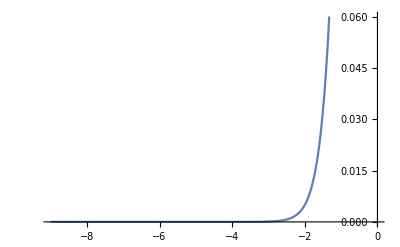
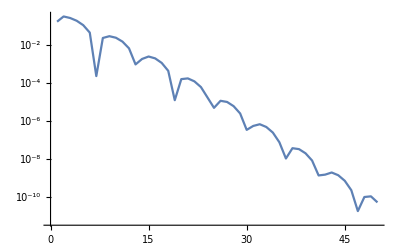
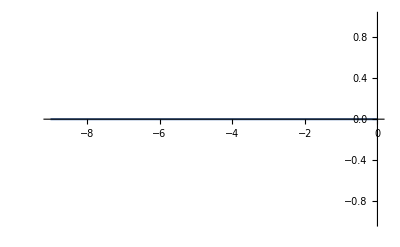
{-Graphics-,3.71124×10^-15,-Graphics-,-Graphics-,-Graphics-,0}

```mathematica
{Plot[Fun[q,Line[{-LL,0}],50][x],{x,-LL,0}],q[-LL],Fun[q,Line[{-LL,0}],50]//DCTPlot,Plot[Fun[qt,Line[{-LL,0}],50][x],{x,-LL,0},PlotRange->All],Fun[qt,Line[{-LL,0}],50]//DCTPlot,qt[-LL]}
```

```mathematica
Poles0=LocatePolesSG[q,qx,qt,0.25,100]
```

{}

```mathematica
Poles = {};
For[i=1,i≤Length[Poles0],i++,
If[Abs[aa[Poles0[[i]]]]<0.2, 
Poles=Join[Poles,{Poles0[[i]]}];
];
];
```

```mathematica
Poles
Abs[Poles]
```

{}

{}

```mathematica
H/@ Poles0
```

{}

```mathematica
H1/@Poles0(*The warning messages may due to calculation of b A outside the region of decaying*)
```

{}

```mathematica
H[10I]
```

Linear solve 1 cond=36.0848

Linear solve 2 cond=8.33108×10^10

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«150»},«49»,«150»} may contain significant numerical errors.

Linear solve 3 cond=8.33648×10^10

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.999996,-0.0000534481,-0.000101875,-0.000158157,-0.000204283,-0.000258784,-0.00030066,«37»,-5.38023×10^-14,-1.758×10^-14,-5.67064×10^-15,-1.83145×10^-15,-5.85393×10^-16,0.,«150»},{«1»},«48»,«150»} may contain significant numerical errors.

Linear solve 4 cond=36.0848

{{0.986141,185124.},{0.0310166,5824.19}}

{{-5890.78,-0.0310166},{187341.,0.986141}}

{{0.63332,118890.},{-120314.,-2.2586×10^10}}

```mathematica
H[10I]
```

Linear solve 1 cond=36.0848

Linear solve 2 cond=8.33108×10^10

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«150»},«49»,«150»} may contain significant numerical errors.

Linear solve 3 cond=8.33648×10^10

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.999996,-0.0000534481,-0.000101875,-0.000158157,-0.000204283,-0.000258784,-0.00030066,«37»,-5.38023×10^-14,-1.758×10^-14,-5.67064×10^-15,-1.83145×10^-15,-5.85393×10^-16,0.,«150»},{«1»},«48»,«150»} may contain significant numerical errors.

Linear solve 4 cond=36.0848

{{0.986141,185124.},{0.0310166,5824.19}}

{{-5890.78,-0.0310166},{187341.,0.986141}}

{{0.63332,118890.},{-120314.,-2.2586×10^10}}

```mathematica
H[0.01I]
```

Linear solve 1 cond=363.459

Linear solve 2 cond=2.38956×10^14

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.994318,0.0113648,-0.0113648,0.0113648,-0.0113648,0.0113648,-0.0113648,«37»,-0.0113648,0.0113648,-0.0113648,0.0113648,-0.0113648,0.0113648,«150»},{-«19»,«50»},«48»,«150»} may contain significant numerical errors.

Linear solve 3 cond=2.38944×10^14

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{1.,-5.34481×10^-6,-0.0000101875,-0.0000158157,-0.0000204283,-0.0000258784,-0.000030066,-0.0000348184,«35»,-1.64452×10^-14,-5.38023×10^-15,-1.758×10^-15,-5.67064×10^-16,0.,0.,0.,«150»},«49»,«150»} may contain significant numerical errors.

Linear solve 4 cond=363.459

{{0.998449,-0.000435213},{-0.000439087,-1.00155}}

{{1.00155,0.000439087},{-0.000359184,0.998449}}

{{0.9969,5.23143×10^-6},{-0.0000811428,-1.00311}}

```mathematica
H[0.15I] (*if*)
```

Linear solve 1 cond=24.6028

Linear solve 2 cond=37.6436

Linear solve 3 cond=37.6436

Linear solve 4 cond=24.6028

{{0.980863,-13.5034},{-0.0543656,-0.271067}}

{{0.271021,0.0543656},{-13.5042,0.980863}}

{{0.965047,-13.2302},{13.2311,-182.426}}

```mathematica
H[0.01I] (*just zero gauge*)
```

Linear solve 1 cond=363.459

Linear solve 2 cond=2.38956×10^14

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.994318,0.0113648,-0.0113648,0.0113648,-0.0113648,0.0113648,-0.0113648,«37»,-0.0113648,0.0113648,-0.0113648,0.0113648,-0.0113648,0.0113648,«150»},{-«19»,«50»},«48»,«150»} may contain significant numerical errors.

Linear solve 3 cond=2.38944×10^14

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{1.,-5.34481×10^-6,-0.0000101875,-0.0000158157,-0.0000204283,-0.0000258784,-0.000030066,-0.0000348184,«35»,-1.64452×10^-14,-5.38023×10^-15,-1.758×10^-15,-5.67064×10^-16,0.,0.,0.,«150»},«49»,«150»} may contain significant numerical errors.

Linear solve 4 cond=363.459

{{0.998449,-0.000435213},{-0.000439087,-1.00155}}

{{1.00155,0.000439087},{-0.000359184,0.998449}}

{{0.9969,5.23143×10^-6},{-0.0000811428,-1.00311}}

```mathematica
H[0.999]
```

Linear solve 1 cond=1.2922

Linear solve 2 cond=1.2922

Linear solve 3 cond=1.2922

Linear solve 4 cond=1.2922

{{0.95611+0.0400909 ⅈ,-0.244061-0.157102 ⅈ},{-0.244061+0.157102 ⅈ,-0.95611+0.0400909 ⅈ}}

{{0.95611-0.0400909 ⅈ,0.244061-0.157102 ⅈ},{-0.244061-0.157102 ⅈ,0.95611+0.0400909 ⅈ}}

{{0.947423-0.0000222042 ⅈ,1.94289×10^-16-0.319982 ⅈ},{1.11022×10^-16+0.319982 ⅈ,-0.947423-0.0000222042 ⅈ}}

```mathematica
Det[{{0.9647960872236874+0.08020409203723336 ⅈ,0.488122227655701+0.0057788130323323805 ⅈ},{0.488122227655701-0.005778813032332436 ⅈ,-0.9647960872236874+0.08020409203723333 ⅈ}}]
```

-1.17556+0. ⅈ

```mathematica
H[1.001]
```

Linear solve 1 cond=1.2922

Linear solve 2 cond=1.29134

Linear solve 3 cond=1.29134

Linear solve 4 cond=1.2922

{{0.95611-0.040091 ⅈ,0.244061-0.157102 ⅈ},{0.244061+0.157102 ⅈ,-0.95611-0.040091 ⅈ}}

{{0.95611+0.040091 ⅈ,-0.244061-0.157102 ⅈ},{0.244061-0.157102 ⅈ,0.95611-0.040091 ⅈ}}

{{0.947423+0.000022182 ⅈ,-1.66533×10^-16-0.319982 ⅈ},{-1.94289×10^-16+0.319982 ⅈ,-0.947423+0.000022182 ⅈ}}

```mathematica
H[0.1(I)](*theres some accuracy problem for very large real z=100*)
```

Linear solve 1 cond=36.0848

Linear solve 2 cond=9.95437×10^16

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.999426,0.00114773,-0.00114773,0.00114773,-0.00114773,0.00114773,-0.00114773,«37»,-0.00114773,0.00114773,-0.00114773,0.00114773,-0.00114773,0.00114773,«150»},«49»,«150»} may contain significant numerical errors.

Linear solve 3 cond=9.7036×10^16

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.999996,-0.0000534481,-0.000101875,-0.000158157,-0.000204283,-0.000258784,-0.00030066,«37»,-5.38023×10^-14,-1.758×10^-14,-5.67064×10^-15,-1.83145×10^-15,-5.85393×10^-16,0.,«150»},{«1»},«48»,«150»} may contain significant numerical errors.

Linear solve 4 cond=36.0848

{{0.986141,-15.873},{-0.0310166,-0.486702}}

{{1.52006,0.0310166},{16.0879,0.986141}}

{{0.973436,-15.6379},{-15.912,254.622}}

```mathematica
Exp[2*50*50.]
```

2.96762838402×10^2171

```mathematica
Chop[Exp[2*50*50.],$MachineEpsilon]
```

2.96762838402×10^2171

```mathematica
H[1000]
```

{{1.00173-0.000373934 ⅈ,-0.0333213-0.0484165 ⅈ},{0.0333213+0.0484165 ⅈ,-0.997042-0.00359322 ⅈ}}

```mathematica
H[0.3I]
```

Linear solve 1 cond=28.9915

Linear solve 2 cond=18.0898

{{0.942203,-7.36701},{6.75797,-53.9027}}

```mathematica
H[1+0.00000001]-H[1-0.0000001]
```

Linear solve 1 cond=1.32187

Linear solve 2 cond=1.32187

Linear solve 1 cond=1.32187

Linear solve 2 cond=1.32187

{{5.55112×10^-16-4.10481×10^-9 ⅈ,-2.498×10^-16+0. ⅈ},{-1.94289×10^-16-1.11022×10^-16 ⅈ,-3.33067×10^-16-4.10481×10^-9 ⅈ}}

```mathematica
H[0.001I]
```

Linear solve 1 cond=8396.85

Power::infy: Infinite expression 1/0. encountered.

Linear solve 2 cond=ComplexInfinity

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«350»},{0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«350»},«47»,{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,«350»},«350»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{1.,-2.9407×10^-7,-5.60659×10^-7,-8.72012×10^-7,-1.13035×10^-6,-1.44205×10^-6,-1.69559×10^-6,-2.0014×10^-6,-2.24482×10^-6,-2.53589×10^-6,-2.75889×10^-6,-3.02164×10^-6,-3.20902×10^-6,-3.42519×10^-6,-3.55788×10^-6,«21»,-2.6583×10^-7,-1.98899×10^-7,-1.46082×10^-7,-1.06581×10^-7,-7.64271×10^-8,-5.44811×10^-8,-3.82149×10^-8,-2.66641×10^-8,-1.83253×10^-8,-1.2535×10^-8,-8.45304×10^-9,-5.67611×10^-9,-3.76043×10^-9,-2.48167×10^-9,«350»},«49»,«350»} may contain significant numerical errors.

{{0.999776,9.83794×10^219},{-2.42067×10^-6,1.77221×10^214}}

### test cond for foward scattering

#### outside unit circle

```mathematica
w=-2I;
el=20;
n=100;
CME[x_]:=Chop[x,$MachineEpsilon];

qf=Fun[q,Line[{-el,0}],n]; (*Forward scattering*)
qtf=Fun[qt,Line[{-el,0}],n];
qxf=qf';(*assume the diff is spectral*)
qfb=Fun[q,Line[{0,el}],n];
qtfb=Fun[qt,Line[{0,el}],n];
qxfb=qfb';

Dm=DerivativeMatrix[qf];      (*this gives the chebyshev differentiation matrix*)
Dmb=DerivativeMatrix[qfb];  (*ie   Dm . Values[qf] = derivative of qf *)
IIm=ReduceDimensionIntegrateMatrix[qf];
IImb=(ReduceDimensionIntegrateMatrix[(qfb//ReverseOrientation)]//Transpose//Reverse//Transpose//Reverse);

id=IdentityMatrix[n];
Q11 = DiagonalMatrix[(I/4/w*(Cos[qf]-1))  //Values];
Q12 = DiagonalMatrix[(I/4/w*Sin[qf]-1/4*(qtf+qxf))  //Values];
Q21 = DiagonalMatrix[(I/4/w*Sin[qf]+1/4*(qtf+qxf)) //Values];
Q22 = DiagonalMatrix[-(I/4/w*(Cos[qf]-1)) //Values];

Qb11 = DiagonalMatrix[(I/4/w*(Cos[qfb]-1))  //Values];
Qb12 = DiagonalMatrix[(I/4/w*Sin[qfb]-1/4*(qtfb+qxfb))  //Values];
Qb21 = DiagonalMatrix[(I/4/w*Sin[qfb]+1/4*(qtfb+qxfb)) //Values];
Qb22 = DiagonalMatrix[-(I/4/w*(Cos[qfb]-1)) //Values];
Jσ3=BlockMatrix[{{0*id,0},{0,-2I IIm}}];
Jσ31=BlockMatrix[{{2I IIm,0},{0,0*id}}];
Jσ3b=BlockMatrix[{{0*id,0},{0,-2I IImb}}];
Jσ31b=BlockMatrix[{{2I IImb,0},{0,0*id}}];
A=BlockMatrix[{{id-IIm.Q11,-IIm.Q12},{-IIm.Q21,id-IIm.Q22}}];
Ab=BlockMatrix[{{id-IImb.Qb11,-IImb.Qb12},{-IImb.Qb21,id-IImb.Qb22}}];

(*A=BlockMatrix[{{id,0},{0,id}}];*)
z=(w-1/w)/4;
On[LinearSolve::luc];
lhs=A+ z*Jσ3;
rhs = Join[IIm.Diagonal[Q11],IIm.Diagonal[Q21]];
Print["Linear solve 1 cond=",Max[SingularValueList[lhs,Tolerance->0]]/Min[SingularValueList[lhs,Tolerance->0]]];
(*Print[SingularValueList[lhs//CME]];*)
illlhs=lhs;
ans0 = LinearSolve[lhs//CME,rhs//CME];

lhs=A+z*Jσ31;
rhs=Join[-IIm.Diagonal[Q12],-IIm.Diagonal[Q22]];
Print["Linear solve 2 cond=",Max[SingularValueList[lhs,Tolerance->0]]/Min[SingularValueList[lhs,Tolerance->0]]];
ans1 = LinearSolve[lhs//CME,rhs//CME];

lhs=Ab+ z*Jσ3b;
rhs = Join[IImb.Diagonal[Qb11],IImb.Diagonal[Qb21]];
Print["Linear solve 3 cond=",Max[SingularValueList[lhs,Tolerance->0]]/Min[SingularValueList[lhs,Tolerance->0]]];ans2 = LinearSolve[lhs//CME,rhs//CME];

lhs=Ab+ z*Jσ31b;
rhs = Join[IImb.Diagonal[Qb12],IImb.Diagonal[Qb22]];
Print["Linear solve 4 cond=",Max[SingularValueList[lhs,Tolerance->0]]/Min[SingularValueList[lhs,Tolerance->0]]];ans3 = LinearSolve[lhs//CME,rhs//CME];
```

Linear solve 1 cond=7.90393×10^11

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«150»},«49»,«150»} may contain significant numerical errors.

Linear solve 2 cond=20.63

Linear solve 3 cond=20.63

Linear solve 4 cond=7.90391×10^11

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.999084,-0.012325,-0.0234996,-0.0365321,-0.0473598,-0.0604589,-0.0712276,-0.0843864,«36»,-0.390008,-0.393259,-0.39359,-0.396049,-0.395585,-0.397247,«150»},«49»,«150»} may contain significant numerical errors.

```mathematica
s1={{ans0[[n]]+1,ans1[[n]]},{ans0[[2n]],ans1[[2n]]-1}}
```

{{0.213023,0.364604},{0.412649,-1.78698}}

#### outside unit circle v2 by integrate the z-1/z part (ignore the 1/w in Q now)

```mathematica
el=20;
n=100;
CME[x_]:=Chop[x,$MachineEpsilon];

 qf=Fun[q,Line[{-el,0}],n]; (*Forward scattering*)
qtf=Fun[qt,Line[{-el,0}],n];
qxf=qf';(*assume the diff is spectral*)
qfb=Fun[q,Line[{0,el}],n];
qtfb=Fun[qt,Line[{0,el}],n];
qxfb=qfb';
xf=Fun[#&,Line[{-el,0}],n];
xfb=Fun[#&,Line[{0,el}],n];

z=(w-1/w)/4;
w1=1;
Dm=DerivativeMatrix[qf];      (*this gives the chebyshev differentiation matrix*)
IIm=ReduceDimensionIntegrateMatrix[qf];
id=IdentityMatrix[n];
Q11 = DiagonalMatrix[(I/4/w*(Cos[qf]-1))  //Values];
Q12 = DiagonalMatrix[(I/4/w*Sin[qf]-1/4*(qtf+qxf))  //Values];
Q21 = DiagonalMatrix[(I/4/w*Sin[qf]+1/4*(qtf+qxf)) //Values];
Q22 = DiagonalMatrix[-(I/4/w*(Cos[qf]-1)) //Values];
Qb11 = DiagonalMatrix[(I/4/w*(Cos[qfb]-1))  //Values];
Qb12 = DiagonalMatrix[(I/4/w*Sin[qfb]-1/4*(qtfb+qxfb))  //Values];
Qb21 = DiagonalMatrix[(I/4/w*Sin[qfb]+1/4*(qtfb+qxfb)) //Values];
Qb22 = DiagonalMatrix[-(I/4/w*(Cos[qfb]-1)) //Values];

Jσ3=BlockMatrix[{{0*id,0},{0,-2I IIm}}];
Jσ31=BlockMatrix[{{2I IIm,0},{0,0*id}}];
Jσ3b=BlockMatrix[{{0*id,0},{0,-2I IImb}}];
Jσ31b=BlockMatrix[{{2I IImb,0},{0,0*id}}];
A=BlockMatrix[{{id-IIm.Q11,-IIm.Q12},{-IIm.Q21,id-IIm.Q22}}];
Ab=BlockMatrix[{{id-IImb.Qb11,-IImb.Qb12},{-IImb.Qb21,id-IImb.Qb22}}];

On[LinearSolve::luc];
lhs=A+ z*Jσ3;
rhs = Join[IIm.Diagonal[Q11],IIm.Diagonal[Q21]];
Print["Linear solve 1 cond=",Max[SingularValueList[lhs,Tolerance->0]]/Min[SingularValueList[lhs,Tolerance->0]]];
(*Print[SingularValueList[lhs//CME]];*)
illlhs=lhs;
ans0a = LinearSolve[lhs//CME,rhs//CME];

expzx=DiagonalMatrix[(Exp[2*I*z*xf])//Values];
iexpzx=DiagonalMatrix[(Exp[-2*I*z*xf])//Values];
expzxb=DiagonalMatrix[(Exp[2*I*z*xfb])//Values];
iexpzxb=DiagonalMatrix[(Exp[-2*I*z*xfb])//Values];

A=BlockMatrix[{{id-iexpzx.IIm.expzx.Q11,-iexpzx.IIm.expzx.Q12},{-IIm.Q21,id-IIm.Q22}}];
lhs=A;
rhs=Join[-iexpzx.IIm.expzx.Diagonal[Q12],-IIm.Diagonal[Q22]];
Print["Linear solve 2 cond=",Max[SingularValueList[lhs,Tolerance->0]]/Min[SingularValueList[lhs,Tolerance->0]]];
ans1a = LinearSolve[lhs//CME,rhs//CME];

Ab=BlockMatrix[{{id-IImb.Qb11,-IImb.Qb12},{-expzx.IImb.iexpzx.Qb21,id-expzx.IImb.iexpzx.Qb22}}];
lhs=Ab;
rhs = Join[IImb.Diagonal[Qb11],expzx.IImb.iexpzx.Diagonal[Qb21]];
Print["Linear solve 3 cond=",Max[SingularValueList[lhs,Tolerance->0]]/Min[SingularValueList[lhs,Tolerance->0]]];
ans2a = LinearSolve[lhs//CME,rhs//CME];

Ab=BlockMatrix[{{id-IImb.Qb11,-IImb.Qb12},{-IImb.Qb21,id-IImb.Qb22}}];
lhs=Ab+ z*Jσ31b;
rhs = Join[IImb.Diagonal[Qb12],IImb.Diagonal[Qb22]];
Print["Linear solve 4 cond=",Max[SingularValueList[lhs,Tolerance->0]]/Min[SingularValueList[lhs,Tolerance->0]]];
ans3a = LinearSolve[lhs//CME,rhs//CME];
```

Linear solve 1 cond=7.90393×10^11

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«150»},«49»,«150»} may contain significant numerical errors.

Linear solve 2 cond=3.03218×10^15

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«150»},«49»,«150»} may contain significant numerical errors.

Linear solve 3 cond=3.03233×10^15

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{1.00004,0.000593851,0.00113144,0.00175338,0.00225388,0.00282649,0.00322441,0.00362439,0.00377643,«34»,4.77519×10^-15,1.37693×10^-15,3.97311×10^-16,0.,0.,0.,0.,«150»},{«1»},«47»,{«1»},«150»} may contain significant numerical errors.

Linear solve 4 cond=7.90391×10^11

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.999084,-0.012325,-0.0234996,-0.0365321,-0.0473598,-0.0604589,-0.0712276,-0.0843864,«36»,-0.390008,-0.393259,-0.39359,-0.396049,-0.395585,-0.397247,«150»},«49»,«150»} may contain significant numerical errors.

```mathematica
Max[Abs[ans0-ans0a]]
Max[Abs[ans1-ans1a]]
Max[Abs[ans2-ans2a]]
Max[Abs[ans3-ans3a]]
```

0.

0.0980649

0.0980649

0.

```mathematica
Max[Abs[expzx]]
```

1.3138×10^16

```mathematica
Exp[2*I*z]
```

0.00640933+0. ⅈ

```mathematica
s1={{ans0[[n]]+1,ans1[[n]]},{ans0[[2n]],ans1[[2n]]-1}}
```

{{0.150186,0.379599},{0.413887,-1.84981}}

```mathematica
IIm.Values[qf]
```

```mathematica
Dimensions[A]
```

{400,400}

#### inside unit circle

```mathematica
w=0.2;
Q11 = DiagonalMatrix[(I/4*w*(Cos[qf]-1))  //Values];
Q12 = DiagonalMatrix[(-I/4*w*Sin[qf]-1/4*(qxf-qtf))  //Values];
Q21 = DiagonalMatrix[(-I/4*w*Sin[qf]+1/4*(qxf-qtf)) //Values];
Q22 = DiagonalMatrix[-(I/4*w*(Cos[qf]-1)) //Values];

Jσ3=BlockMatrix[{{0*id,0},{0,-2I IIm}}];
Jσ31=BlockMatrix[{{2I IIm,0},{0,0*id}}];
A=BlockMatrix[{{id+IIm.Q11,+IIm.Q12},{+IIm.Q21,id+IIm.Q22}}];
(*A=BlockMatrix[{{id,0},{0,id}}];*)

z=(w-1/w)/4;
On[LinearSolve::luc];
lhs=A+ z*Jσ3;
rhs = Join[-IIm.Diagonal[Q11],-IIm.Diagonal[Q21]];
Print["Linear solve 1 cond=",Max[SingularValueList[lhs,Tolerance->0]]/Min[SingularValueList[lhs,Tolerance->0]]];
(*Print[SingularValueList[lhs//CME]];*)
illlhs=lhs;
ans0 = LinearSolve[lhs//CME,rhs//CME];

lhs=A+z*Jσ31;
rhs=Join[IIm.Diagonal[Q12],IIm.Diagonal[Q22]];
Print["Linear solve 2 cond=",Max[SingularValueList[lhs,Tolerance->0]]/Min[SingularValueList[lhs,Tolerance->0]]];
ans1 = LinearSolve[lhs//CME,rhs//CME];
```

Linear solve 1 cond=1213.5

Linear solve 2 cond=1213.5

#### inside unit circle with partial integration

```mathematica
xf=Fun[#&,Line[{-el,0}],n];
xfb=Fun[#&,Line[{0,el}],n];
Q11 = DiagonalMatrix[(I/4*w*(Cos[qf]-1))  //Values];
Q12 = DiagonalMatrix[(-I/4*w*Sin[qf]-1/4*(qxf-qtf))  //Values];
Q21 = DiagonalMatrix[(-I/4*w*Sin[qf]+1/4*(qxf-qtf)) //Values];
Q22 = DiagonalMatrix[-(I/4*w*(Cos[qf]-1)) //Values];

Jσ3=BlockMatrix[{{0*id,0},{0,-2I IIm}}];
Jσ31=BlockMatrix[{{2I IIm,0},{0,0*id}}];
A=BlockMatrix[{{id+IIm.Q11,+IIm.Q12},{+IIm.Q21,id+IIm.Q22}}];
(*A=BlockMatrix[{{id,0},{0,id}}];*)

z=(w-1/w)/4;
expzx=DiagonalMatrix[(Exp[2*I*z*xf])//Values];
iexpzx=DiagonalMatrix[(Exp[-2*I*z*xf])//Values];
expzxb=DiagonalMatrix[(Exp[2*I*z*xfb])//Values];
iexpzxb=DiagonalMatrix[(Exp[-2*I*z*xfb])//Values];

On[LinearSolve::luc];
lhs=A+ z*Jσ3;
rhs = Join[-IIm.Diagonal[Q11],-IIm.Diagonal[Q21]];
Print["Linear solve 1 cond=",Max[SingularValueList[lhs,Tolerance->0]]/Min[SingularValueList[lhs,Tolerance->0]]];
(*Print[SingularValueList[lhs//CME]];*)
illlhs=lhs;
ans2 = LinearSolve[lhs//CME,rhs//CME];

A=BlockMatrix[{{id+iexpzx.IIm.expzx.Q11,+iexpzx.IIm.expzx.Q12},{+IIm.Q21,id+IIm.Q22}}];
lhs=A;
rhs=Join[+iexpzx.IIm.expzx.Diagonal[Q12],+IIm.Diagonal[Q22]];
Print["Linear solve 2 cond=",Max[SingularValueList[lhs,Tolerance->0]]/Min[SingularValueList[lhs,Tolerance->0]]];
ans3 = LinearSolve[lhs//CME,rhs//CME];
```

Linear solve 1 cond=1213.5

Linear solve 2 cond=1.252

```mathematica
Max[Abs[ans0-ans2]]
Max[Abs[ans1-ans3]]
```

0.

6.031×10^-15

```mathematica
n=200;
lhs=IdentityMatrix[n]-10*ReduceDimensionIntegrateMatrix[Fun[q&,Line[{0,1}],n]];
Max[SingularValueList[lhs,Tolerance->0]]/Min[SingularValueList[lhs,Tolerance->0]]
```

92646.2

```mathematica
Abs[Eigenvalues[lhs]]
```

```mathematica
Dimensions[lhs]
```

{10,10}

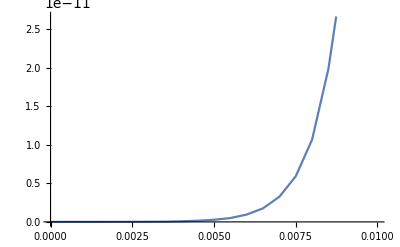

```mathematica
xmax=0.01;
TablePlot[Abs[H[I x][[1,2]]],{x,0,xmax,xmax/20}]
```

```mathematica
H[0.05I]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.997468,0.00506313,-0.00506313,0.00506313,-0.00506313,0.00506313,-0.00506313,«37»,-0.00506313,0.00506313,-0.00506313,0.00506313,-0.00506313,0.00506313,«150»},{«1»},«47»,{«1»},«150»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.999996,-0.0000593851,-0.000113144,-0.000175338,-0.000225388,-0.000282649,-0.000322441,-0.000362439,-0.000377643,«33»,-1.63005×10^-15,-4.77519×10^-16,0.,0.,0.,0.,0.,0.,«150»},{«1»},«47»,{«1»},«150»} may contain significant numerical errors.

{{0.985826,-0.0874431},{0.0965624,-1.02294}}

```mathematica
H[0.01I]
```

{{0.997099,-2.24518×10^-11},{1.99465×10^-10,-1.00291}}

```mathematica
H[0.0001I]
```

{{0.999971,3.70612×10^-17},{-5.24502×10^-17,-1.00003}}

```mathematica
zz=0.01I;
H[zz]
```

{{0.997099,-2.24518×10^-11},{1.99465×10^-10,-1.00291}}

```mathematica
Inverse[{{1-Cos[q[0]],-Sin[q[0]]},{-Sin[q[0]],Cos[q[0]]-1+2-2zz^2}}].{{1-Cos[q[0]],-Sin[q[0]]},{-Sin[q[0]],Cos[q[0]]-1}}
```

{{1.+0. ⅈ,-1.83049×10^6+0. ⅈ},{-5.82077×10^-11+0. ⅈ,-1.×10^6+0. ⅈ}}

```mathematica
(Cos[q[0.]]+1)/(Sin[q[0]]^2+(Cos[q[0.]]+1)^2)*Sin[q[0]]
```

0.420735

```mathematica
Simplify[(Cos[x]+1)/(Sin[x]^2+(Cos[x]+1)^2)]
```

1/2

```mathematica
xx=0.;
Sqrt[1/2]*Sin[q[xx]]/Sqrt[1-Cos[q[xx]]]
Sqrt[1/2]*Sqrt[1-Cos[q[xx]]]
```

0.877583

0.479426

```mathematica
Sqrt[1/2]*Sin[q[xx]]/Sqrt[1+Cos[q[xx]]]
-Sqrt[1/2]*Sqrt[1+Cos[q[xx]]]
```

0.479426

-0.877583

```mathematica
Cos[q[0.]/2]
Sin[q[0.]/2]
```

0.877583

0.479426

```mathematica
FullSimplify[Sin[x]/Sqrt[1+cos[x]]]
```

Sin[x]/(√(1+cos[x]))

#### Reflection coeff

```mathematica
ρ[k_]:=Piecewise[{{0,k==0},{bb[k]/aa[k],k!=0}}];
ρb[k_]:=Piecewise[{{0,k==0},{-BB[k]/AA[k],k!=0}}];
(*ρ[k_]:=Abs[k]^2*Sech[Abs[k]^2];*)
rad=0.8;
bigN=100;
el=25;
SetParams[.1,rad,10.^(-7),30,bigN,el];
(*"SetParams[ν,rad,globalTol,smallN,bigN] sets the parameters for the rest of the code:
	ν: half of width of strip of analyticity
	rad: radius of soliton contours
	globalTol: contour truncation tolerance
	smallN: small number of collocation points
	bigN: big number of collocation points";if no truncations is done, then more points is required to get sufficient accuracy*)
ν=Getnu[];
h[k_]:=2/(1+Abs[Abs[k]/2+1])^2;
Setrsamp[h];
Settimeflag[False];
c=SetScatteringData[aa,bb1,ρ,ρb,Poles](*output the norming constant*)
```

{}

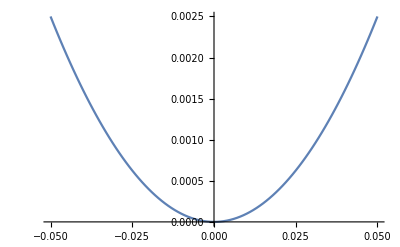
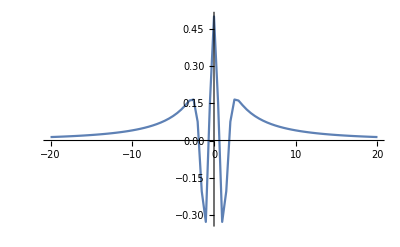
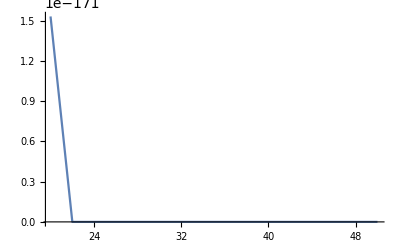

```mathematica
{TablePlot[Abs[ρ[x]],{x,-0.1/2,0.1/2,0.001},PlotRange->All],TablePlot[Abs[h[x]]-Abs[ρ[x]],{x,-20,20,0.5},PlotRange->All],
TablePlot[Abs[ρ[x]],{x,20,50,2},PlotRange->All]}
```

```mathematica
hhh=50;
h[hhh]-Abs[ρ[hhh]]
Abs[ρ[500]]
Abs[ρ[40]]
Abs[ρ[30]]
Abs[ρ[25]]
```

0.00274217

0.0538004

1.01657×10^-9

5.23765×10^-8

1.19627×10^-6

## Plotting: timestring outputs relevant computation times and region information

```mathematica
qSGgeneral=NotebookDirectory[]<>"qSGm";(*file name*)
```

```mathematica
(*load qSGm if already calculated*)
qSGm//Clear;
Get["qSGm"];
```

Get::noopen: Cannot open qSGm.

```mathematica
qSG//Clear;
qSG[x_,t_]:=qSG[x,t]=SGAuto[x,t];(*qSG is the solution to the rhp at z=0, the transform qSG[xx,tt].{{1,0},{0,-1}}.Inverse[qSG[xx,tt]] gives the solution q to the sine-Gordon in the form {{cos q, sin q},{sin q, -cos q}}*)
```

```mathematica
myacos[x_]:=Piecewise[{{ArcCos[Re[x[[1,1]]]],ArcSin[Re[x[[1,2]]]]>0},{2Pi-ArcCos[Re[x[[1,1]]]],ArcSin[Re[x[[2,1]]]]≤0}}];
```

```mathematica
xx=0.5;
tt=0;
qSG[xx,tt]
timestring
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix … may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{0.999991-9.37672×10^-6 ⅈ,-0.00011877-0.000126215 ⅈ,-0.000226289-0.000240473 ⅈ,-0.000350676-0.000372657 ⅈ,-0.000450776-0.000479031 ⅈ,-0.000565297-0.00060073 ⅈ,-0.000644882-0.000685303 ⅈ,-0.000724877-0.000770313 ⅈ,-0.000755286-0.000802628 ⅈ,-0.000768151-0.000816299 ⅈ,«32»,-3.26009×10^-15-3.46444×10^-15 ⅈ,-9.55038×10^-16-1.0149×10^-15 ⅈ,-2.75386×10^-16-2.92647×10^-16 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,«150»},«49»,«150»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix … may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

$Aborted

timestring

```mathematica
Det[qSG[xx,tt]](*should be 1*)
```

1.+2.51825×10^-17 ⅈ

```mathematica
ans=qSG[xx,tt].{{1,0},{0,-1}}.Inverse[qSG[xx,tt]]
```

{{0.922929-1.44048×10^-17 ⅈ,0.38497+7.74006×10^-17 ⅈ},{0.38497-8.33237×10^-18 ⅈ,-0.922929+1.44048×10^-17 ⅈ}}

```mathematica
ans1=ans.{{1,0},{0,-1}}.Inverse[ans]
```

{{0.773638-9.03957×10^-18 ⅈ,-0.633628-5.13413×10^-17 ⅈ},{-0.633628+2.92673×10^-17 ⅈ,-0.773638+9.03957×10^-18 ⅈ}}

```mathematica
Cos[q[xx]]-ans[[1,1]]
Sin[q[xx]]-ans[[1,2]]
Sin[q[xx]]-ans[[2,1]]
```

-0.216565+1.44048×10^-17 ⅈ

0.322879-7.74006×10^-17 ⅈ

0.322879+8.33237×10^-18 ⅈ

```mathematica
{out,phi,rhp1,rhp2,ttime}=SG[0][0.5,0];
```

```mathematica
phi[-1-0.1I]
```

{{0.973497+0.00514234 ⅈ,-0.344331-0.030768 ⅈ},{-0.212988-0.0452623 ⅈ,1.10122+0.0169241 ⅈ}}

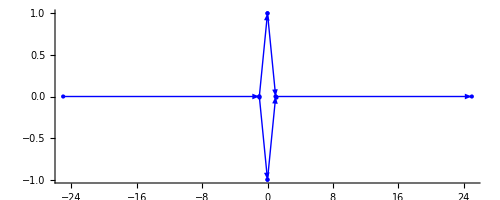

```mathematica
domainOutput
```

```mathematica
zz=(-0.5+0.5I);
phi[zz+0.000001I]-phi[zz-0.000001I].P[0.5,0][zz]
```

{{-5.5057×10^-9-2.06259×10^-8 ⅈ,-1.0052×10^-7-2.34287×10^-8 ⅈ},{7.46354×10^-8-2.93426×10^-7 ⅈ,3.88509×10^-10+1.07044×10^-8 ⅈ}}

```mathematica
zz=(-0.5-0.5I);
phi[zz+0.000001I]-phi[zz-0.000001I].M[0.5,0][zz]
```

{{-3.88509×10^-10+1.07044×10^-8 ⅈ,7.49247×10^-8+2.96678×10^-7 ⅈ},{-1.0052×10^-7+2.34287×10^-8 ⅈ,-2.39987×10^-8-9.72244×10^-9 ⅈ}}

```mathematica
rhp1[[1]][[1,2]][-1.5]
```

0.458942+0.0970207 ⅈ

```mathematica
Cauchy[RHSolve[MakeListFun[J[0][xx,tt]]],2+I]+IdentityMatrix[2]
```

{{1.02666-0.0157937 ⅈ,-0.106397-0.0671987 ⅈ},{-0.00442163+0.208449 ⅈ,0.988226-0.00611047 ⅈ}}

```mathematica
zz=0.55I;
M[xx,tt][zz].P[xx,tt][zz]-G[xx,tt][zz]
```

{{0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ}}

```mathematica
P[xx,tt][(-1+I)/2](*not well posed in the lower half plane*)
```

{{1,0},{0.302373+0.0379947 ⅈ,1}}

```mathematica
M[xx,tt][(-1-I)/2].P[xx,tt][(-1-I)/2]-G[xx,tt][(-1-I)/2]
```

{{0.+2.77556×10^-17 ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.+0. ⅈ}}

```mathematica
H[-1.61I]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«150»},«49»,«150»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {«1»} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

{{1.26732,-0.414477},{0.414477,-0.924624}}

```mathematica
tt=0;
G[xx,tt][10]
```

{{1.00023+0. ⅈ,-0.00908565+0.0123402 ⅈ},{-0.00908565-0.0123402 ⅈ,1}}

```mathematica
{out,phi,rhp1,rhp2,tt}=SG[0][0.5,0];
```

```mathematica
phi[I+0.000000001I]-phi[I-0.000000001I]
```

{{1.98304×10^-9+1.21431×10^-17 ⅈ,8.34418×10^-11-2.25514×10^-17 ⅈ},{-1.3731×10^-8+1.38778×10^-17 ⅈ,7.40041×10^-12-8.67362×10^-19 ⅈ}}

```mathematica
phi[I-0.00001]
```

{{0.97181+5.63957×10^-7 ⅈ,-0.141+4.17211×10^-7 ⅈ},{0.300914-3.30574×10^-6 ⅈ,0.985348+3.70024×10^-8 ⅈ}}

```mathematica
θ[x_,t_][z_]:= Piecewise[{{0,z==0},{2*I/4 ((z+1/z)t+(z-1/z)x ),z≠0}}];    
exppt[x_,t_][z_]:=Piecewise[{{0,z==0},{Exp[θ[x,t][z]],z≠0}}];
P[x_,t_][k_]:=({{1, 0}, {ρ[k] exppt[x,t][k], 1}});
```

```mathematica
P[0.5,0][I]
```

{{1,0},{-1.37507×10^-8+0. ⅈ,1}}

```mathematica
ρ[1.3I]
```

-0.220326

```mathematica
Grhp1[[1]][[1,2]][-0.6]
```

0.232512-0.486601 ⅈ

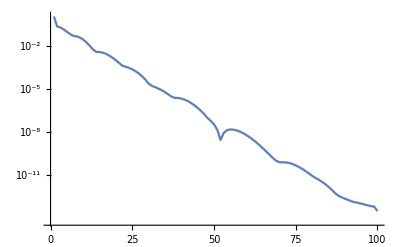
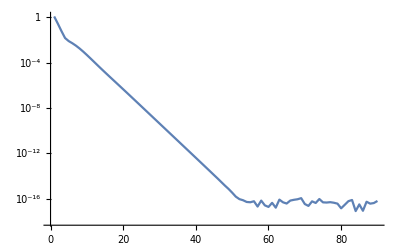
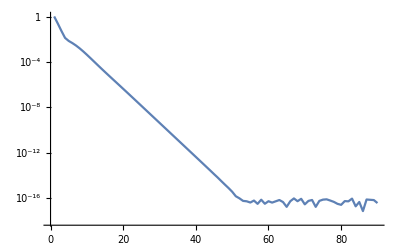
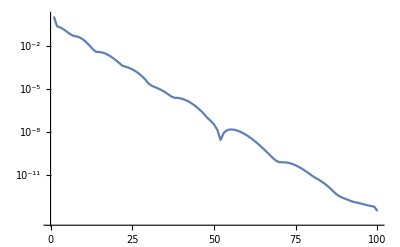
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
DCTPlot/@ Grhp1
```

```mathematica
DCTPlot/@ Grhp2
```

Grhp2

```mathematica
mRHWellPosed[Grhp1]
```

((1. | 7.01461×10^-10-7.35782×10^-10 ⅈ
7.01461×10^-10+7.35782×10^-10 ⅈ | 1.) | -40.
(1. | 0
0 | 1.) | -1.
(1. | 0
0 | 1.) | 0.-1. ⅈ
(1. | 0
0 | 1.) | 0.+1. ⅈ
(1. | 0
0 | 1.) | 1.
(1. | -7.01461×10^-10-7.35782×10^-10 ⅈ
-7.01461×10^-10+7.35782×10^-10 ⅈ | 1.) | 40.)

```mathematica
θ[x_,t_][z_]:= Piecewise[{{0,z==0},{2*I/4 ((z+1/z)t+(z-1/z)x ),z≠0}}];
```

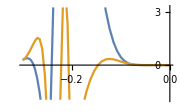

```mathematica
r1=Fun[cc[ρ[cc[#]]]*Exp[-θ[1,0][#]]&,Line[{-ν-I*ν,-(1+I)*0.001}],60]
```

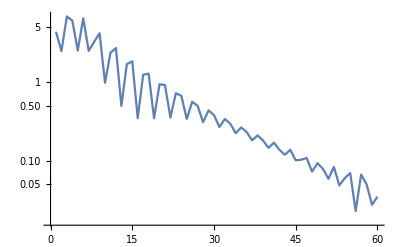

```mathematica
DCTPlot[r1]
```

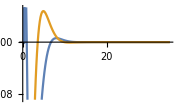

Thread::tdlen: Objects of unequal length in {«1»}+{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«50»} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

Diagonal::list: List expected at position 1 in ….

General::stop: Further output of Diagonal::list will be suppressed during this calculation.

$Aborted

$Aborted

```mathematica
r4=Fun[cc[ρ[cc[#]]]*Exp[-θ[1,0][#]]&,Line[{-I*ν,35-I*ν}],200]
```

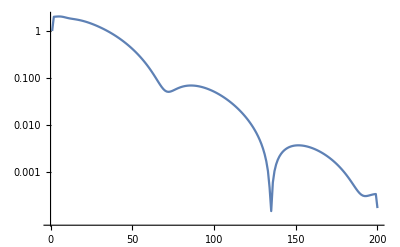

```mathematica
DCTPlot[r4]
```

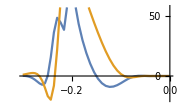

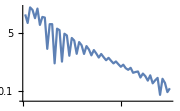

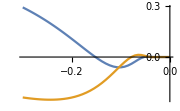

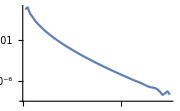

```mathematica
r2=Fun[cc[ρ[cc[#]]]&,Line[{-ν-I*ν,-(1+I)*0.001}],60]
DCTPlot[r2]
r3=Fun[Exp[-θ[1,0][#]]&,Line[{-ν-I*ν,-(1+I)*0.001}],60]
DCTPlot[r3]
```

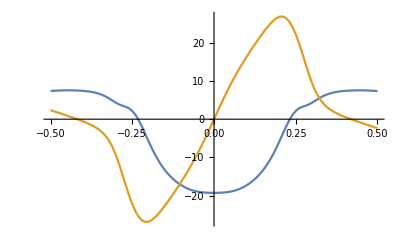

```mathematica
TablePlot[{Re[ρ[x+0.4I]],Im[ρ[x+0.4I]]},{x,-0.5,0.5,0.01},PlotRange->All]
```

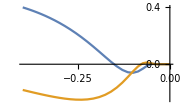

```mathematica
tt1=Fun[Exp[-θ[1,0][#]]&,Line[{-ν-I*ν,(-1-I)*0.0001}],40]
```

```mathematica
θ[1,0][0.00001*Exp[I Pi*3/2]]
```

50000.+0. ⅈ

```mathematica
θ[1,0][-0.00001]
```

0.+50000. ⅈ

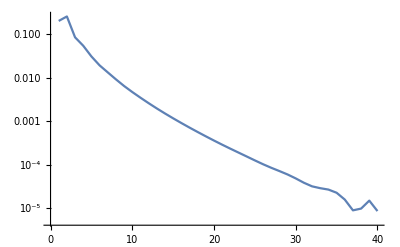

```mathematica
DCTPlot[tt1]
```

```mathematica
DCTPlot[Fun[Exp[-θ[1,0][#]]&,Line[{-ν-I*ν,0}],100]]
```

$Aborted

$Aborted

```mathematica
myacos[ans]
q[xx]
```

4.53638

4.53638

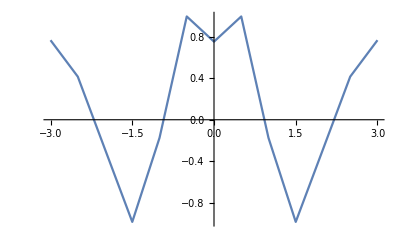

```mathematica
TablePlot[Cos[q[x]],{x,-3,3,0.5},PlotRange->All]
```

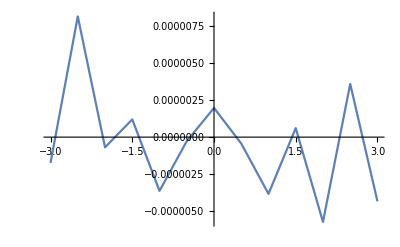

```mathematica
Monitor[TablePlot[Re[1+2*qSG[x,0][[1,2]]*qSG[x,0][[2,1]]]-Cos[q[x]],{x,-3,3,0.5},PlotRange->All],timestring]
```

#### Compare with finite difference method

```mathematica
xmin=-5;
xmax=5;
dx=1.;
tmin=0.;
tmax=2;
dt=1;
lmax=10.//N;
```

```mathematica
(*FD solve nonlinear eq*)
FDsolver[NN_]:=Module[{},
ddt=1/NN/2;
ddx=1/NN;
xxx=Range[-lmax,lmax-ddx,ddx];
ttt=Range[tmin,tmax,ddt];
nq0=Table[q[x],{x,-lmax,lmax-ddx,ddx}];(*even number of points*)
nqt0=Table[qt[x],{x,-lmax,lmax-ddx,ddx}];(*even number of points*)
nx=Round[2*lmax/ddx]; 
nt=Round[tmax/ddt]+1;
qfd=ConstantArray[0,{nx,nt}];
For[j=1,j≤nx,j=j+1,
qfd[[j,1]]=nq0[[j]];
qfd[[j,2]]=nq0[[j]]+nqt0[[j]]*ddt;
];
For[n=1,n≤ nt-2,n++,
For[j=2,j≤nx-1,j=j+1,
qfd[[j,n+2]]=(ddt/ddx)^2*(qfd[[j+1,n+1]]-2qfd[[j,n+1]]+qfd[[j-1,n+1]])-ddt^2*Sin[qfd[[j,n+1]]]+2qfd[[j,n+1]]-qfd[[j,n]]
]
];
iqfd=Interpolation[Flatten[Table[{{xxx[[j]],ttt[[n]]},qfd[[j,n]]},{j,1,nx},{n,1,nt}],1]];
{qfd,iqfd}
]
```

```mathematica
Timing[qfd=FDsolver[10][[1]]][[1]]
```

0.09375

```mathematica
(*plot fd sol*)
Manipulate[
{ListLinePlot[Cases[Table[{xxx[[k]],Re[Cos[qfd[[k,t]]]]},{k,1,nx,Round[nx/200]+1}],{x_,y_}/;-lmax≤x≤lmax],PlotRange->{-1,1}],ListLinePlot[Cases[Table[{xxx[[k]],Re[qfd[[k,t]]]},{k,1,nx,Round[nx/200]+1}],{x_,y_}/;-lmax≤x≤lmax],PlotRange->All]},{t,1,nt,Round[nt/30]+1}]
```

```mathematica
(*plot interpolated fd sol*)
Manipulate[TablePlot[Cos[iqfd[x,t]],{x,xmin,xmax,dx},PlotRange->{-1,1},InterpolationOrder->1,PlotStyle->Thick],{t,tmin,tmax,dt}]
```

```mathematica
(*compute ist sol*)
Monitor[qSGm=Table[qSG[x,t],{x,xmin,xmax,dx},{t,tmin,tmax,dt}],timestring];
Save[qSGgeneral,qSGm];
```

```mathematica
(*no monitor version*)
qSGm=Table[qSG[x,tt],{x,xmin,xmax,dx},{tt,tmin,tmax,dt}];
Save[qSGgeneral,qSGm];
```

```mathematica
ix=Range[xmin,xmax,dx];
it=Range[tmin,tmax,dt];
icosq=Interpolation[Flatten[Table[{{ix[[j]],it[[n]]},(qSGm[[j,n]].{{1,0},{0,-1}}.Inverse[qSGm[[j,n]]])[[1,1]]},{j,1,Length[ix]},{n,1,Length[it]}],1]];
```

Interpolation::inhr: Requested order is too high; order has been reduced to {3,2}.

```mathematica
(*plot ist sol*)
Manipulate[
TablePlot[Re[icosq[x,t]],{x,xmin,xmax,dx},PlotRange->{-1,1},InterpolationOrder->1,PlotStyle->Thick],{t,tmin,tmax,dt}]
```

```mathematica
iqfd10=FDsolver[10][[2]];
iqfd20=FDsolver[20][[2]];
iqfd40=FDsolver[40][[2]];
iqfd80=FDsolver[80][[2]];
iqfd160=FDsolver[160][[2]];
```

```mathematica
(*difference between fd and ist*)
Manipulate[
{TablePlot[{icosq[x,t],Cos[iqfd10[x,t]]},{x,xmin,xmax,dx},PlotRange->{-1.1,1.1},InterpolationOrder->1,PlotStyle->Thick],TablePlot[Abs[icosq[x,t]-Cos[iqfd10[x,t]]],{x,xmin,xmax,dx},PlotRange->All,InterpolationOrder->1,PlotStyle->Thick],
TablePlot[Abs[icosq[x,t]-Cos[iqfd20[x,t]]],{x,xmin,xmax,dx},PlotRange->All,InterpolationOrder->1,PlotStyle->Thick],
TablePlot[Abs[icosq[x,t]-Cos[iqfd40[x,t]]],{x,xmin,xmax,dx},PlotRange->All,InterpolationOrder->1,PlotStyle->Thick],
TablePlot[Abs[icosq[x,t]-Cos[iqfd80[x,t]]],{x,xmin,xmax,dx},PlotRange->All,InterpolationOrder->1,PlotStyle->Thick],
TablePlot[Abs[icosq[x,t]-Cos[iqfd160[x,t]]],{x,xmin,xmax,dx},PlotRange->All,InterpolationOrder->1,PlotStyle->Thick]},{t,tmin,tmax,dt}]
```

```mathematica
(*solve linearized eq  utt-uxx+u=0*)
Manipulate[
dd=0.2;
xx=Range[-lmax,lmax-dd,dd];
nq0=Table[q[x],{x,-LL,LL-dd,dd}];(*even number of points*)
nqt0=Table[qt[x],{x,-LL,LL-dd,dd}];(*even number of points*)
w=Pi/LL*Join[Range[0,Length[nq0]/2], Range[-Length[nq0]/2+1,-1]];
nhq0=Fourier[nq0];
nhqt0=Fourier[nqt0];
(*nhqt=Quiet[nhq0*Exp[I/w*tt]*I*w/.Indeterminate->0.];*)
nhqt=(nhq0*Cos[Sqrt[1+w^2]*tt]+nhqt0/Sqrt[1+w^2]*Sin[Sqrt[1+w^2]*tt])/.Indeterminate->0.;
nqt=InverseFourier[nhqt];
ListLinePlot[Cases[Table[{xx[[k]],Cos[Re[nqt[[k]]]]},{k,1,Length[nq0]}],{x_,y_}/;-LL≤x≤LL],PlotRange->{-1,1}],{tt,0,10,0.1/8}]
```

### Debug

```mathematica
ListPlot3D[Flatten[Table[{x,y,Abs[G[0,0][x+I y][[1,2]]]},{x,-1/2,1/2,0.1},{y,-1/2,1/2,0.1}],1],AxesLabel->{x,y,z},PlotRange->All]
```

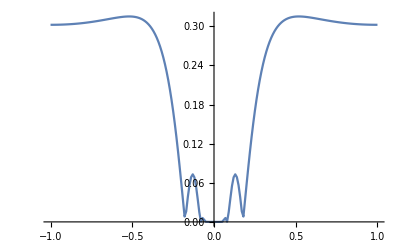

```mathematica
TablePlot[Abs[G[0,0][z][[2,1]]],{z,-1,1,0.01},PlotRange->All]
```

```mathematica
{out,phi,rhp1,rhp2,tt}=SG[0][0,0];
```

Private`PoleList[0,0]

```mathematica
out
```

{{1.-2.61924×10^-17 ⅈ,-9.07193×10^-7+1.61446×10^-14 ⅈ},{1.05074×10^-6+1.38608×10^-14 ⅈ,1.-3.20662×10^-17 ⅈ}}

```mathematica
phi[0]
```

{{1.-2.61924×10^-17 ⅈ,-9.07193×10^-7+1.61446×10^-14 ⅈ},{1.05074×10^-6+1.38608×10^-14 ⅈ,1.-3.20662×10^-17 ⅈ}}

```mathematica
rhp2
```

Private`rhp2$8428

```mathematica
RHSolved//Clear;
RHSolved[X_]:=RHSolved[X]=RHSolve[X];
RHSolved[{}]:=0.;
RHSolution[X_][z_]:=Cauchy[X//RHSolved,z]+IdentityMatrix[2];
```

```mathematica
RHSolution[rhp1][0]
```

{{0.540253-2.41751×10^-14 ⅈ,-0.84145+1.80897×10^-14 ⅈ},{0.841514+1.52933×10^-14 ⅈ,0.540317+2.72282×10^-14 ⅈ}}

```mathematica
RHSolution[rhp2][0]
```

{{1+Cauchy[0.,0],Cauchy[0.,0]},{Cauchy[0.,0],1+Cauchy[0.,0]}}

```mathematica
r[k_]:=ρ[k];
θ[x_,t_][z_]:=2 I (-t/4/z+x z);
rb[k_]:= cc[r[cc[k]]];
rbsamp[k_]:= cc[rsamp[cc[k]]];
τsamp[k_]:=1+ rsamp[k]cc[rsamp[cc[k]]];

G[x_,t_][z_]:=({{1+r[z]rb[z], rb[z]Exp[-θ[x,t][k]]}, {r[z] Exp[θ[x,t][k]], 1}});
G[_,_][_?InfinityQ]:=({{1., 0}, {0, 1.}});
```

```mathematica
J[0][0,0]
```

{{G[0,0][#1]&,G[0,0][#1]&},{Line[{-100,0}],Line[{0,100}]},{40,40}}

```mathematica
J[1][-10,0]
```

{{U[-10,0][#1]&,U[-10,0][#1]&,Private`DD[#1]&,L[-10,0][#1]&,L[-10,0][#1]&,Private`P[-10,0][#1]&,Private`P[-10,0][#1]&,Private`M[-10,0][#1]&,Private`M[-10,0][#1]&},{Line[{0.+0.4 ⅈ,99.6+0.4 ⅈ}],Line[{99.6+0.4 ⅈ,100}],Line[{0,100}],Line[{0.-0.4 ⅈ,99.6-0.4 ⅈ}],Line[{99.6-0.4 ⅈ,100}],Line[{100,100.4+0.4 ⅈ}],Line[{100.4+0.4 ⅈ,200.+0.4 ⅈ}],Line[{100,100.4-0.4 ⅈ}],Line[{100.4-0.4 ⅈ,200.-0.4 ⅈ}]},{20,20,20,20,20,20,20,20,20}}

```mathematica
Jadapt[1][-10,0]
```

{{U[-10,0][#1]&,Private`DD[#1]&,L[-10,0][#1]&},{Line[{0.+0.4 ⅈ,7.9125+0.4 ⅈ}],Line[{0,5.8625}],Line[{0.-0.4 ⅈ,7.9125-0.4 ⅈ}]},{40,40,40}}

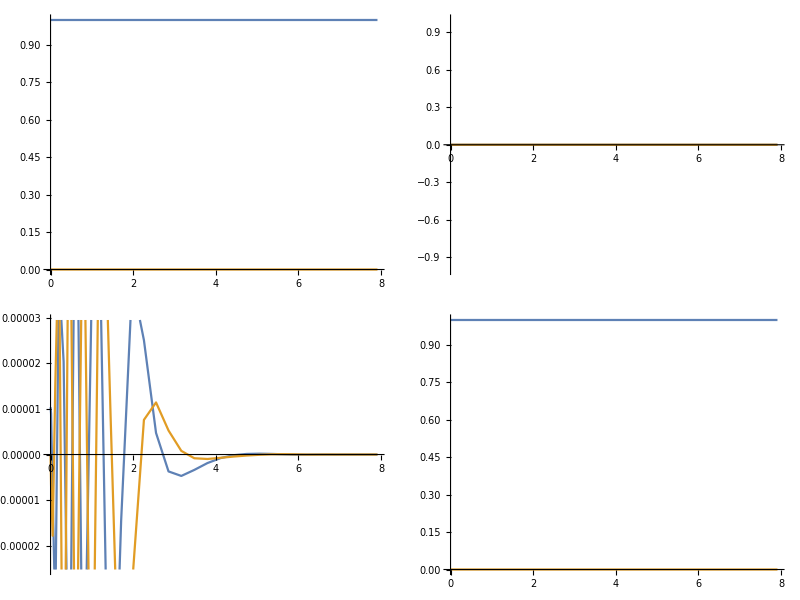
(-Graphics-)

```mathematica
ff=Fun[L[-10,0][#1]&,Line[{0.-0.4 ⅈ,7.912499999999998-0.4 ⅈ}],40]
```

```mathematica
L[-10,0][0]
```

{{1,0},{0.499885,1}}

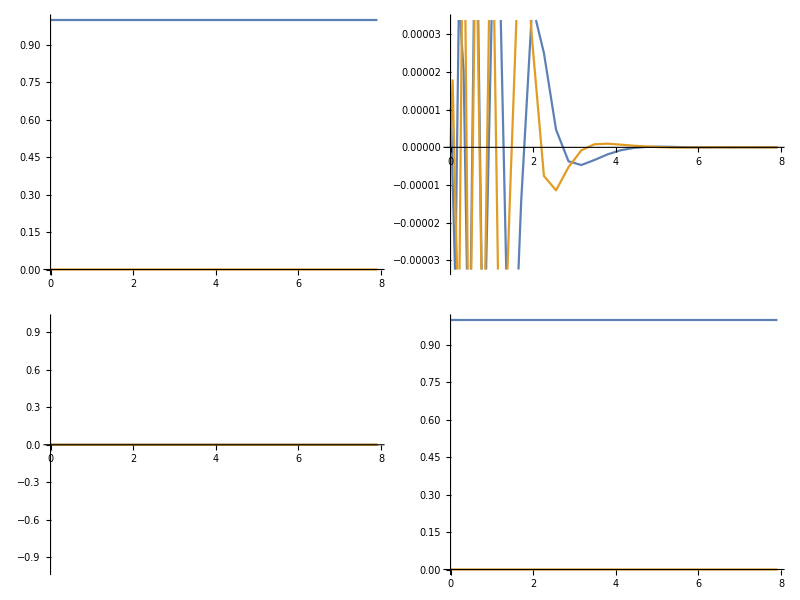
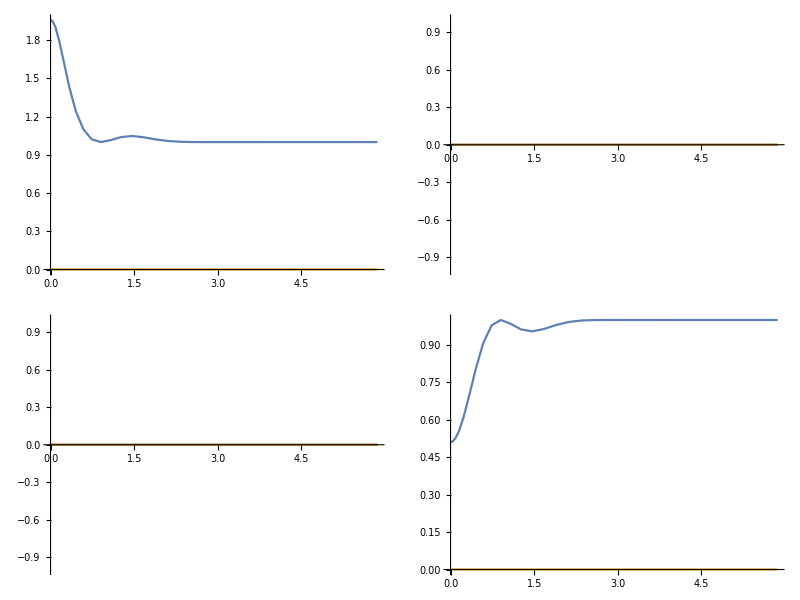
{(-Graphics-),(-Graphics-),(-Graphics-)}

```mathematica
GG=Jadapt[1][-10,0]//MakeListFun
```

```mathematica
Grhp1[[1]][-1]
```

{{1.+2.71019×10^-8 ⅈ,-13985.2-18010.7 ⅈ},{0.+0. ⅈ,1.+1.49136×10^-8 ⅈ}}

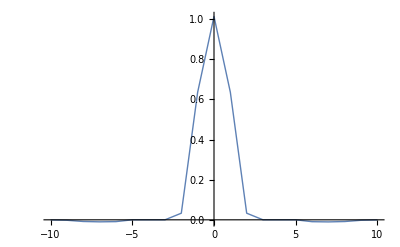

```mathematica
(* Focusing *)
Monitor[TablePlot[qNLS[x,0.0]//Re,{x,-10,10,1.},PlotRange->All,InterpolationOrder->1,PlotStyle->Thick],timestring]
```

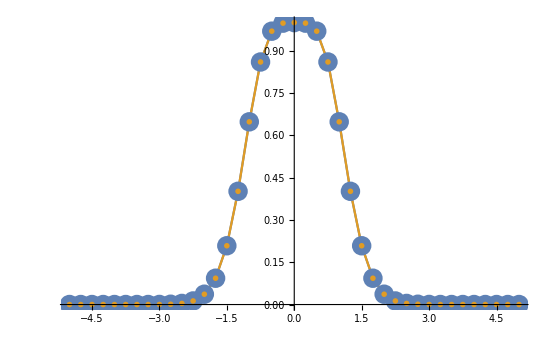

```mathematica
TablePlot[{qNLS[x,0.]//Re,Sech[x^2]},{x,-10,10,1.},PlotMarkers->{{●,20},{"x",30}}]
```

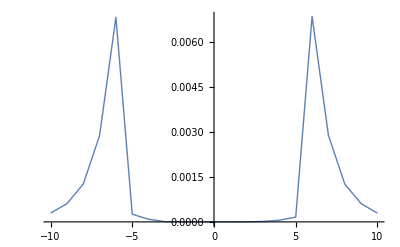

```mathematica
TablePlot[Abs[qNLS[x,0.]-Sech[x^2]],{x,-10,10,1.},PlotRange->All,InterpolationOrder->1,PlotStyle->Thick]
```

```mathematica
TablePlot[Abs[qNLS[x,0.0]-Sech[x^2]]/Sech[x^2],{x,-10,10,1.},PlotRange->All,InterpolationOrder->1,PlotStyle->Thick]
```

```mathematica
(* Defocusing *)
Monitor[TablePlot[qmKdV[x,1.]//Re,{x,-20,10,.25},PlotRange->All,InterpolationOrder->1,PlotStyle->Thick],timestring]
```

$Aborted

RuleDelayed::rhs: Pattern mu_ appears on the right-hand side of rule pp[mu_,nn_]:>(pp[mu_,nn_]=LocatePolesSG[q,qx,qt,mu,nn]).

RuleDelayed::rhs: Pattern nn_ appears on the right-hand side of rule pp[mu_,nn_]:>(pp[mu_,nn_]=LocatePolesSG[q,qx,qt,mu,nn]).

$Aborted

LinearSolve::matrix: Argument {{«1»}+{(0.+0.000510204 ⅈ) (-1/Part[«2»]+{}⟦2⟧),(0.-0.00102041 ⅈ) (-1/Part[«2»]+{}⟦2⟧),(0.+0.00102041 ⅈ) (-1/Part[«2»]+{}⟦2⟧),(0.-0.00102041 ⅈ) (-1/Part[«2»]+{}⟦2⟧),«44»,(0.+0.00102041 ⅈ) (-1/Part[«2»]+{}⟦2⟧),(0.-0.000510204 ⅈ) (-1/Part[«2»]+{}⟦2⟧),«50»},«49»,«50»} at position 1 is not a non-empty rectangular matrix.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. π ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. π ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. π ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Part::partw: Part 50 of LinearSolve[{{1-{«50»}.DiagonalMatrix[«1»],«49»,«1»}+{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«50»},{«1»}+{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«50»},«47»,{«1»}+{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«17»,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«50»},«50»},«1»] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

LinearSolve::matrix: Argument {{«1»}+{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«50»},«49»,«50»} at position 1 is not a non-empty rectangular matrix.

General::stop: Further output of LinearSolve::matrix will be suppressed during this calculation.

Inverse::matsq: Argument {{{«1»},{{1-Dot[«2»],-{«50»}.DiagonalMatrix[«1»],-{«50»}.DiagonalMatrix[«1»],-{«50»}.DiagonalMatrix[«1»],-{«50»}.DiagonalMatrix[«1»],-{«50»}.DiagonalMatrix[«1»],-{«50»}.DiagonalMatrix[«1»],«38»,-{«50»}.DiagonalMatrix[«1»],-{«50»}.DiagonalMatrix[«1»],-{«50»}.DiagonalMatrix[«1»],-{«50»}.DiagonalMatrix[«1»],-{«50»}.DiagonalMatrix[«1»],«1»}+{«1»},«49»,«50»}},{«1»⟦51⟧,«1»}} at position 1 is not a non-empty square matrix.

$Aborted[]